Load the JSON file.  What we get is a recursive set of replacement rules.
The keys are strings.

```mathematica
jfile =Import["v:\\chuck\\Documents\\FUSOR\\Experiments\\fusor-2021-04-25T22-45-22-160Z_pumpdown 1.json"]
```

{base-timestamp→1619390722159,instant→2021-04-25T22:45:22.160Z,log→{{device→<reset>,data→{},servertime→1619390722159},222039,{}}}
 |  |  |  |

```mathematica
log="log"/.jfile
```

{{device→<reset>,data→{},servertime→1619390722159},{device→RP,data→{rp_in→{value→False,vartime→0},rp_stat→{value→False,vartime→1141151},devicetime→1141156},servertime→1619390722170},222038,{}}
 |  |  |  |

```mathematica
Length[log]
```

222041

```mathematica
baseServerTime="base-timestamp"/.jfile
```

1619390722159

What sort of records are in the log?
These are defined by the “device”.  Here are all the types we see:

```mathematica
DeleteDuplicates[("device"/.#)&/@log]
```

{<reset>,RP,PN-JUNCTION,HV-LOWSIDE,PIRANI,TMP,VARIAC,GAS,Heartbeat,Command,<promote>,Comment,Login,device}

If we’d like a mix of record types, we can do this.
I don’t know if this is useful, as opposed to extracting types individually.

```mathematica
gp=Select[log,MemberQ[{"GAS","PIRANI"},("device"/.#)]&]
```

{{device→PIRANI,data→{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139461},3,pa→{value→0.,vartime→1139587},devicetime→1139819},servertime→1619390722206},60451,{1}}
 |  |  |  |

```mathematica
ListDevices[jfile_List]:=Module[{log},
log="log"/.jfile;
Select[DeleteDuplicates[("device"/.#)&/@log],#≠"device"&]
]
```

```mathematica
ListDevices[jfile]
```

{<reset>,RP,PN-JUNCTION,HV-LOWSIDE,PIRANI,TMP,VARIAC,GAS,Heartbeat,Command,<promote>,Comment,Login}

```mathematica
GetDeviceLog[deviceName_String,jfile_List]:=Module[{log},
log="log"/.jfile;
Select[log,("device"/.#)==deviceName&]
]
```

```mathematica
Take[GetDeviceLog["TMP",jfile],3]
```

{{device→TMP,data→{tmp→{value→False,vartime→0},tmp_stat→{value→False,vartime→1140964},lowspeed→{value→False,vartime→0},pump_curr_amps→{value→0.,vartime→1140964},pump_freq→{value→0.,vartime→1140964},devicetime→1140974},servertime→1619390722214},{device→TMP,data→{tmp→{value→False,vartime→0},tmp_stat→{value→False,vartime→1141093},lowspeed→{value→False,vartime→0},pump_curr_amps→{value→0.,vartime→1141093},pump_freq→{value→0.,vartime→1141093},devicetime→1141102},servertime→1619390722340},{device→TMP,data→{tmp→{value→False,vartime→0},tmp_stat→{value→False,vartime→1141221},lowspeed→{value→False,vartime→0},pump_curr_amps→{value→0.,vartime→1141221},pump_freq→{value→0.,vartime→1141221},devicetime→1141230},servertime→1619390722473}}

```mathematica
GetDeviceData[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->10];
getAllVars[dev,timeFit]
]
```

```mathematica
pd=GetDeviceData["PIRANI",jfile]
```

{{p1,p2,p3,p4,pa_adc,pa},{{{10.14,490.},{10.14,490.},{10.14,490.},28123,{3.63729916×10^6,212.},{3.63729916×10^6,212.},{3.63769757×10^6,212.}},{1},3,{1}}}
 |  |  |  |

```mathematica
pd[[2,2,;;10]]
```

{{-312.197,5.4},{72.2,5.4},{72.2,5.4},{72.2,5.4},{476.617,5.4},{476.617,5.4},{476.617,5.4},{857.01,5.4},{857.01,5.4},{857.01,5.4}}

```mathematica
Head[jfile]
```

List

```mathematica
gas=Select[log,("device"/.#)=="GAS"&];
gas[[1]]
```

{device→GAS,data→{sol_in→{value→False,vartime→6586425},sol_stat→{value→False,vartime→7058601},nv_in→{value→0,vartime→6923709},nv_stat→{value→0,vartime→7058601},nv_angle→{value→0,vartime→6923710},devicetime→7058606},servertime→1619390722244}

```mathematica
pirani=Select[log,("device"/.#)=="PIRANI"&];
pirani[[1]]
```

{device→PIRANI,data→{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139461},p3→{value→771.,vartime→1139516},p4→{value→771.2,vartime→1139587},pa_adc→{value→0,vartime→1139587},pa→{value→0.,vartime→1139587},devicetime→1139819},servertime→1619390722206}

```mathematica
piraniServerTimes=("servertime"/.#&/@pirani)-baseServerTime;
Take[piraniServerTimes,10]
```

{47,129,317,444,576,706,833,960,1092,1218}

```mathematica
piraniDeviceTimes="devicetime"/.("data"/.#)&/@pirani;
Take[piraniDeviceTimes,10]
```

{1139819,1139901,1140091,1140218,1140345,1140476,1140603,1140730,1140861,1140988}

```mathematica
piraniAdjust=piraniServerTimes[[1]]-piraniDeviceTimes[[1]];
Take[piraniDeviceTimes+piraniAdjust,10]
```

{47,129,319,446,573,704,831,958,1089,1216}

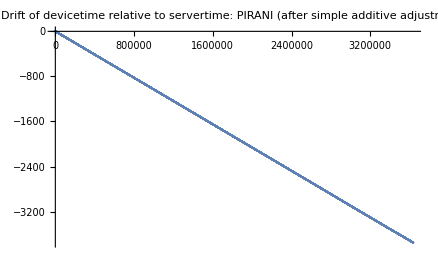

```mathematica
ListPlot[Transpose[{piraniServerTimes,(piraniDeviceTimes+piraniAdjust)-piraniServerTimes}],
PlotLabel->"Drift of devicetime relative to servertime: PIRANI\n(after simple additive adjustment)"]
```

```mathematica
piraniFit = LinearModelFit[Transpose[{piraniDeviceTimes,piraniServerTimes}],x,x,WorkingPrecision->10];
```

```mathematica
Normal[piraniFit]
```

-1.140950444×10^6+1.001033161 x

```mathematica
piraniFitResiduals=piraniFit/@piraniDeviceTimes-piraniServerTimes;
```

```mathematica
Mean[piraniFitResiduals]
```

0.

```mathematica
StandardDeviation[piraniFitResiduals]
```

1.39

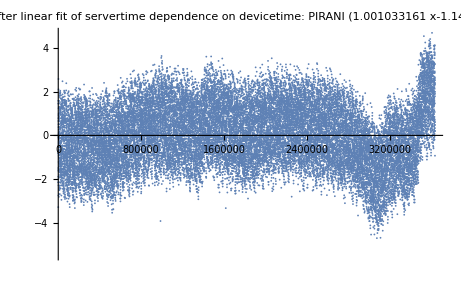

```mathematica
ListPlot[Transpose[{piraniServerTimes,piraniFitResiduals}],
PlotLabel->"Residuals after linear fit of servertime dependence on devicetime: PIRANI\n"Normal[piraniFit]]
```

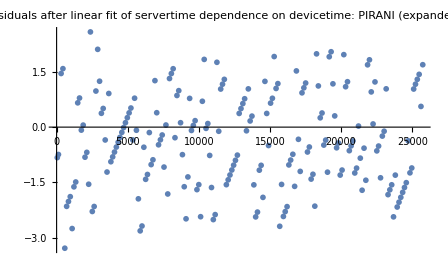

```mathematica
ListPlot[Take[Transpose[{piraniServerTimes,piraniFitResiduals}],200],
PlotLabel->"Residuals after linear fit of servertime dependence on devicetime: PIRANI\n(expanded scale)"]
```

```mathematica
gasServerTimes=("servertime"/.#&/@gas)-baseServerTime;
Take[gasServerTimes,10]
```

{85,85,198,310,422,534,647,760,872,984}

```mathematica
gasDeviceTimes="devicetime"/.("data"/.#)&/@gas;
Take[gasDeviceTimes,10]
```

{7058606,7058628,7058742,7058854,7058966,7059079,7059191,7059304,7059416,7059529}

```mathematica
gasFit = LinearModelFit[Transpose[{gasDeviceTimes,gasServerTimes}],x,x,WorkingPrecision->10];
```

```mathematica
Normal[gasFit]
```

-7.058592594×10^6+1.000006695 x

```mathematica
gasFitResiduals=gasFit/@gasDeviceTimes-gasServerTimes;
```

```mathematica
StandardDeviation[gasFitResiduals]
```

1.2

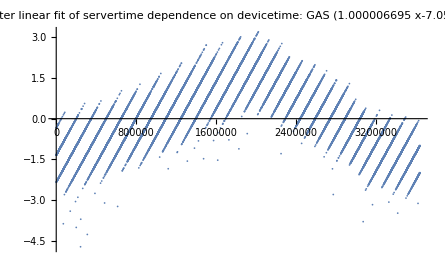

```mathematica
ListPlot[Transpose[{gasServerTimes,gasFitResiduals}],
PlotLabel->"Residuals after linear fit of servertime dependence on devicetime: GAS\n"Normal[gasFit]]
```

```mathematica
gasAdjust=gasServerTimes[[1]]-gasDeviceTimes[[1]];
Take[gasDeviceTimes+gasAdjust,10]
```

{85,107,221,333,445,558,670,783,895,1008}

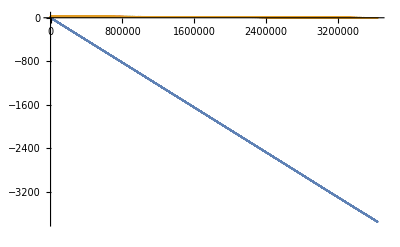

```mathematica
ListPlot[{Transpose[{piraniServerTimes,(piraniDeviceTimes+piraniAdjust)-piraniServerTimes}],Transpose[{gasServerTimes,(gasDeviceTimes+gasAdjust)-gasServerTimes}]}]
```

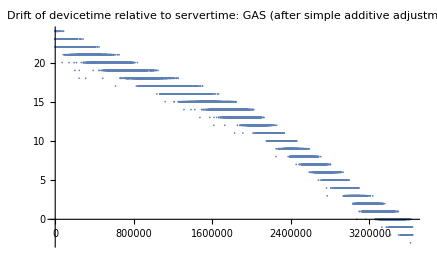

```mathematica
ListPlot[Transpose[{gasServerTimes,(gasDeviceTimes+gasAdjust)-gasServerTimes}],
PlotLabel->"Drift of devicetime relative to servertime: GAS\n(after simple additive adjustment)"]
```

```mathematica
Take[(gasDeviceTimes+gasAdjust)-gasServerTimes,100]
```

{0,22,23,23,23,24,23,23,23,24,22,23,24,23,23,23,22,24,24,23,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,23,23,22,24,22,24,22,23,23,23,23,23,23,22,23,22,23,23,23,23,23,22,23,23,23,23,22,23,22,23,23,24,23,23,23,24,23,23,23,22,22,23,22,23,23,23,23,23,23,23,23,23,23,23,23,23,22,24,22,23,22,23}

```mathematica
gas[[1]]
```

{device→GAS,data→{sol_in→{value→False,vartime→6586425},sol_stat→{value→False,vartime→7058601},nv_in→{value→0,vartime→6923709},nv_stat→{value→0,vartime→7058601},nv_angle→{value→0,vartime→6923710},devicetime→7058606},servertime→1619390722244}

```mathematica
gas[[2]]
```

{device→GAS,data→{sol_in→{value→False,vartime→6586425},sol_stat→{value→False,vartime→7058622},nv_in→{value→0,vartime→6923709},nv_stat→{value→0,vartime→7058622},nv_angle→{value→0,vartime→6923710},devicetime→7058628},servertime→1619390722244}

```mathematica
piraniTimeDiffs=piraniDeviceTimes-piraniServerTimes;
```

```mathematica
rp=Select[log,("device"/.#)=="RP"&];
Take[rp,5]
```

{{device→RP,data→{rp_in→{value→False,vartime→0},rp_stat→{value→False,vartime→1141151},devicetime→1141156},servertime→1619390722170},{device→RP,data→{rp_in→{value→False,vartime→0},rp_stat→{value→False,vartime→1141258},devicetime→1141263},servertime→1619390722289},{device→RP,data→{rp_in→{value→False,vartime→0},rp_stat→{value→False,vartime→1141269},devicetime→1141275},servertime→1619390722289},{device→RP,data→{rp_in→{value→False,vartime→0},rp_stat→{value→False,vartime→1141376},devicetime→1141382},servertime→1619390722391},{device→RP,data→{rp_in→{value→False,vartime→0},rp_stat→{value→False,vartime→1141483},devicetime→1141488},servertime→1619390722498}}

```mathematica
Length[rp]
```

33261

```mathematica
Length[Select[log,("device"/.#)=="TMP"&]]
```

28173

```mathematica
pirani[[1]]
```

{device→PIRANI,data→{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139461},p3→{value→771.,vartime→1139516},p4→{value→771.2,vartime→1139587},pa_adc→{value→0,vartime→1139587},pa→{value→0.,vartime→1139587},devicetime→1139819},servertime→1619390722206}

```mathematica
Normal[piraniFit]
```

-1.140950444×10^6+1.001033161 x

```mathematica
d="data"/.pirani[[1]]
```

{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139461},p3→{value→771.,vartime→1139516},p4→{value→771.2,vartime→1139587},pa_adc→{value→0,vartime→1139587},pa→{value→0.,vartime→1139587},devicetime→1139819}

```mathematica
Select[d,Head[#[[2]]]==List&]
```

{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139461},p3→{value→771.,vartime→1139516},p4→{value→771.2,vartime→1139587},pa_adc→{value→0,vartime→1139587},pa→{value→0.,vartime→1139587}}

```mathematica
Table[i[[1]],{i,Select[d,Head[#[[2]]]==List&]}]
```

{p1,p2,p3,p4,pa_adc,pa}

```mathematica
getVar[s_String,deviceLog_List,timeFit_FittedModel]:=
Module[{dList,vList},
dList=("data"/.#)& /@ deviceLog;
vList = (s/.#)& /@ dList;
{timeFit @("vartime"/.#), ("value"/.#)}& /@ vList
]
```

```mathematica
getVar["p1",pirani,piraniFit]
```

{{10.14,490.},{10.14,490.},28125,{3.63729916×10^6,212.},{3.63769757×10^6,212.}}
 |  |  |  |

```mathematica
getAllVars[deviceLog_List,timeFit_FittedModel]:=
Module[{varList},
varList=Table[i[[1]],{i,Select["data"/.deviceLog[[1]],Head[#[[2]]]==List&]}];
{varList,Table[getVar[v,deviceLog,timeFit],{v,varList}]}
]
```

```mathematica
piraniData=getAllVars[pirani,piraniFit];
```

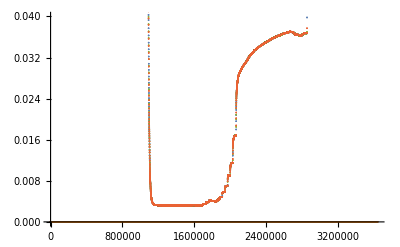

```mathematica
ListPlot[piraniData[[2]],PlotRange->{Automatic,{0,0.04}}]
```

```mathematica
Dimensions[piraniData[[2]]]
```

{6,28129,2}

```mathematica
Take[Flatten[piraniData[[2]],{{2},{1,3}}],3]
```

{{10.14,490.,-312.197,5.4,-257.14,771.,-186.07,771.2,-186.07,0,-186.07,0.},{10.14,490.,72.2,5.4,-257.14,771.,-186.07,771.2,-186.07,0,-186.07,0.},{10.14,490.,72.2,5.4,153.28,771.,213.35,771.2,213.35,0,213.35,0.}}

```mathematica
piraniFlat=Flatten[piraniData[[2]],{{2},{1,3}}];
```

```mathematica
Export["c:\\temp\\pirani.csv",piraniFlat]
```

c:\temp\pirani.csv

```mathematica
Take[pirani,3]
```

{{device→PIRANI,data→{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139461},p3→{value→771.,vartime→1139516},p4→{value→771.2,vartime→1139587},pa_adc→{value→0,vartime→1139587},pa→{value→0.,vartime→1139587},devicetime→1139819},servertime→1619390722206},{device→PIRANI,data→{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139845},p3→{value→771.,vartime→1139516},p4→{value→771.2,vartime→1139587},pa_adc→{value→0,vartime→1139587},pa→{value→0.,vartime→1139587},devicetime→1139901},servertime→1619390722288},{device→PIRANI,data→{p1→{value→490.,vartime→1139783},p2→{value→5.4,vartime→1139845},p3→{value→771.,vartime→1139926},p4→{value→771.2,vartime→1139986},pa_adc→{value→0,vartime→1139986},pa→{value→0.,vartime→1139986},devicetime→1140091},servertime→1619390722476}}

```mathematica
Head[pirani]
```

List

```mathematica
dt=(piraniFit /@ piraniDeviceTimes)-piraniServerTimes
```

{-0.827,-0.742,1.45,28123,2.33,0.48,0.612}
 |  |  |  |

```mathematica
StandardDeviation[dt]
```

1.39

```mathematica
Max[dt]
```

4.69

```mathematica
Min[dt]
```

-9.791

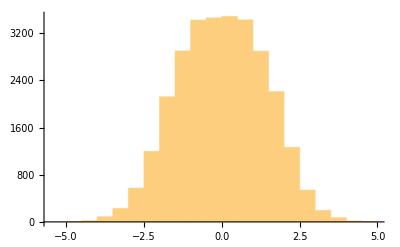

```mathematica
Histogram[dt]
```

```mathematica
dtg=(gasFit/@gasDeviceTimes)-gasServerTimes
```

{-24.34,-2.34,-1.3,32318,-1.99,-0.99,-1.99}
 |  |  |  |

```mathematica
StandardDeviation[dtg]
```

1.2

```mathematica
Max[dtg]
```

3.2

```mathematica
Min[dtg]
```

-24.34

```mathematica
Min[Drop[dtg,1]]
```

-4.71

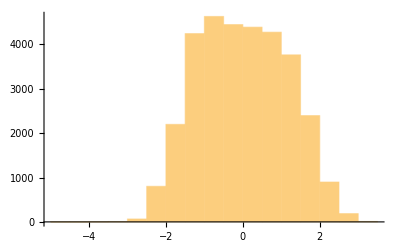

```mathematica
Histogram[Drop[dtg,1]]
```

```mathematica
gas[[;;3]]
```

{{device→GAS,data→{sol_in→{value→False,vartime→6586425},sol_stat→{value→False,vartime→7058601},nv_in→{value→0,vartime→6923709},nv_stat→{value→0,vartime→7058601},nv_angle→{value→0,vartime→6923710},devicetime→7058606},servertime→1619390722244},{device→GAS,data→{sol_in→{value→False,vartime→6586425},sol_stat→{value→False,vartime→7058622},nv_in→{value→0,vartime→6923709},nv_stat→{value→0,vartime→7058622},nv_angle→{value→0,vartime→6923710},devicetime→7058628},servertime→1619390722244},{device→GAS,data→{sol_in→{value→False,vartime→6586425},sol_stat→{value→False,vartime→7058736},nv_in→{value→0,vartime→6923709},nv_stat→{value→0,vartime→7058736},nv_angle→{value→0,vartime→6923710},devicetime→7058742},servertime→1619390722357}}